# AMS-511 Foundations of Quantitative Finance

## Fall 2018 — Assignment 12

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Lookback Options

### Overview

An lookback option is a path dependent option whose value is based on some function of the underlying’s price history over the life of the option/ rather than the price at expiry. Read the Wikipedia article https://en.wikipedia.org/wiki/Lookback_option which describes these options in detail.

The particular case that is the focus of this assignment is the lookback put with floating price:

P(T)=max[max_t [S(t)]-S(T),0]=S_max-S(T)

### FinancialDerivative[ ]

The corresponding Mathematica solution is identified as a {“LookbackFloating”, “European”, “Put”}. Use the various documentation and help functions with Mathematica to determine the required parameters for FinancialDerivative[ ].

## Assignment

Create a function that uses Monte Carlo to estimate the value of an lookback floating European put using the same parameters (where appropriate) as those in Assignment 11. Perform the same tasks as in Assignment 11: Evaluate the option price for S(0)=$95.00, then compute its values for S[0] from $80.00 to $120.00, inclusive, in increments of $5.00 and compare them to the results from FinancialDerivative[ ].

```mathematica
FinancialDerivative[{"LookbackFloating", "European", "Put"}, {"Expiration"->1.,"Inception"->0.,"MaxSoFar"->80.},{"CurrentPrice"->80.,"Volatility"->0.10,"InterestRate"->0.02}]
```

5.77036

```mathematica
xGeneratePrice[nNowPrice_,nVolatility_,nRiskFree_,nTimeStep_]:=nNowPrice Exp[(nRiskFree-nVolatility^2/2.)nTimeStep]Exp[ nVolatility RandomVariate[NormalDistribution[0,√nTimeStep]]]
```

```mathematica
xLookbackFloatingEuroPutOptMonteCarlo[nNowPrice_,nVolatility_,nExpiry_,nInception_,nRiskFree_,iSamples_,iTimeSteps_]:={Mean[#],StandardDeviation[#]/√iSamples}&[ 
Exp[-nRiskFree nExpiry]Table[(Max[#]-Last[#])&[NestList[xGeneratePrice[#, nVolatility, nRiskFree,nExpiry/iTimeSteps]&,nNowPrice,iTimeSteps]],iSamples]
];
```

```mathematica
xLookbackFloatingEuroPutOptMonteCarlo[80,0.1,1,0,0.02,100,100]
```

{4.8523,0.37277}

{82.6337,{{{80.,5.05361},{85.,5.64475},{90.,5.86253},{95.,6.02508},{100.,6.84032},{105.,7.08268},{110.,6.94002},{115.,7.40066},{120.,8.04361}},{{80.,5.43187},{85.,6.04665},{90.,6.28738},{95.,6.45927},{100.,7.32106},{105.,7.58933},{110.,7.47774},{115.,7.93653},{120.,8.60464}},{{80.,5.81013},{85.,6.44855},{90.,6.71223},{95.,6.89346},{100.,7.8018},{105.,8.09597},{110.,8.01545},{115.,8.4724},{120.,9.16567}}}}

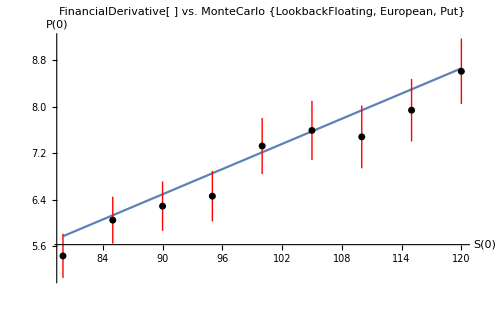

```mathematica
Timing[mnSim=Transpose@Block[
{sol},
Table[
sol=xLookbackFloatingEuroPutOptMonteCarlo[price,0.1,1,0,0.02,500,500];
{{price,sol⟦1⟧-1.96sol⟦2⟧},{price,sol⟦1⟧},{price,sol⟦1⟧+1.96sol⟦2⟧}},
{price,80.,120.,5.}
]
]]
Show[
ListLinePlot[Table[{price,FinancialDerivative[{"LookbackFloating", "European", "Put"}, {"Expiration"->1.,"Inception"->0.,"MaxSoFar"->price},{"CurrentPrice"->price,"Volatility"->0.10,"InterestRate"->0.02}]},{price,80,120,5}],PlotLabel->Style["FinancialDerivative[ ] vs. MonteCarlo\n{LookbackFloating, European, Put}",FontSize->16],AxesLabel->(Style[#,FontSize->14]&/@{"S(0)","P(0)"})],
ListPlot[mnSim,PlotStyle->{{PointSize[0]},{Black,PointSize[0.01]},{PointSize[0]}},Filling->{1->{3}},FillingStyle->Red],PlotRange->All,ImageSize->500]
```

The floating lookback European put option has a closed solution, so Mathematica always gives the same answer. My monte carlo implementation is mostly accurate to within a 95% confidence interval, but occasionally the FinancialDerivative solution is outside that confidence interval. It may be that the time steps and sample size are too low, but it takes my computer approximately 90 seconds to generate a price using 500 time steps and 500 samples.